```mathematica
AppendTo[$Path,NotebookDirectory[]];
Needs["PenroseTilingFunctions`"]
```

```mathematica
Inflate[starseed,1]
```

{{{0.809017+0.587785 ⅈ,0,0.618034},fat},{{0.618034,1,0.809017+0.587785 ⅈ},skinny},{{1.30902+0.951057 ⅈ,1,0.809017+0.587785 ⅈ},fat},{{0.809017+0.587785 ⅈ,0,0.190983+0.587785 ⅈ},fat},{{0.190983+0.587785 ⅈ,0.309017+0.951057 ⅈ,0.809017+0.587785 ⅈ},skinny},{{1.30902+0.951057 ⅈ,0.309017+0.951057 ⅈ,0.809017+0.587785 ⅈ},fat},{{-0.309017+0.951057 ⅈ,0,0.190983+0.587785 ⅈ},fat},{{0.190983+0.587785 ⅈ,0.309017+0.951057 ⅈ,-0.309017+0.951057 ⅈ},skinny},{{-0.5+1.53884 ⅈ,0.309017+0.951057 ⅈ,-0.309017+0.951057 ⅈ},fat},{{-0.309017+0.951057 ⅈ,0,-0.5+0.363271 ⅈ},fat},{{-0.5+0.363271 ⅈ,-0.809017+0.587785 ⅈ,-0.309017+0.951057 ⅈ},skinny},{{-0.5+1.53884 ⅈ,-0.809017+0.587785 ⅈ,-0.309017+0.951057 ⅈ},fat},{{-1.,0,-0.5+0.363271 ⅈ},fat},{{-0.5+0.363271 ⅈ,-0.809017+0.587785 ⅈ,-1.},skinny},{{-1.61803,-0.809017+0.587785 ⅈ,-1.},fat}}

```mathematica
Midpoints[{A_,B_,C_}]:=1/2{B+A,B+C,A+C}
```

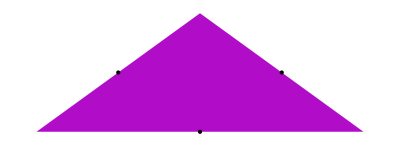

```mathematica
Show[See@{unitfat},Graphics[Point/@Coor@Midpoints[unitfat]]]
```

```mathematica
PathTriangles[{{A_,P_,B_,C_},t_}]:=If[t=="fat",{{A,P,C},{B,C,P}},{{A,B,C},{A,P,B}}]
```

```mathematica
??IfFat
```

T if the triangle is fat, F if skinny

IfFat[t_,T_,F_]:=If[Last[t]==fat,T,F]

Rhomb[{{a_,b_,c_},f_}]:={{a,a-c+b,b,c},f}

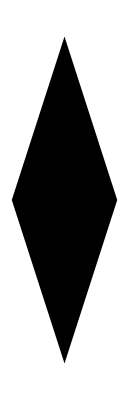

```mathematica
Graphics[(Polygon/@Coor/@PathTriangles@Rhomb@unitskinny)]
```

```mathematica
TestPoints:=Graphics@{Yellow,EdgeForm[Black],{Triangle@Coor@ #,{PointSize[Large],Transpose[{{Red,Green,Blue},Point/@Coor@#}]}}}&
```

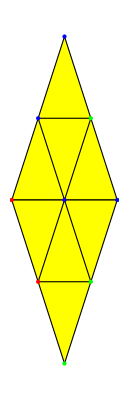

```mathematica
Show[TestPoints/@(PathTriangles@Rhomb@unitskinny),TestPoints/@(Midpoints/@PathTriangles@Rhomb@unitskinny)]
```

```mathematica
Midpoints/@PathTriangles@Rhomb@unitskinny
```

{{0.,0.25+0.769421 ⅈ,-0.25+0.769421 ⅈ},{-0.25-0.769421 ⅈ,0.25-0.769421 ⅈ,0.}}

```mathematica
SharedSide[list_,element_]:=Select[list,MemberQ[element]]
FindNextTriangle[list_,prev_,midpoint_]:=DeleteCases[SharedSide[list,midpoint],prev]
```

```mathematica
Midpoints/@PathTriangles@Rhomb@unitskinny
FindNextTriangle[%,%[[1]],0.]
```